### Definiciones

```mathematica
Needs["Carlos`"]
(*Needs["Quantum`"]*)
```

```mathematica
IndicesToChange[PreIndex_,PostIndex_,TargetParticle_,NumberOfParticles_]:=Table[FromDigits[Join[IntegerDigits[PreIndex,4,NumberOfParticles-TargetParticle-1],{Iterator},IntegerDigits[PostIndex,4,TargetParticle]],4],{Iterator,0,3}]
```

```mathematica
AllDigits[NumberOfDigits_,Base_]:=IntegerDigits[#,Base,NumberOfDigits]&/@(Range[Power[Base,NumberOfDigits]]-1)
AllDigits[NumberOfDigits_]:=AllDigits[NumberOfDigits,4]
```

```mathematica
ApplyAToCuasiparticle[psi_,TargetParticle_Integer,a_]:=Module[{NumberOfParticles,IndicesInQuestion,reglas,psitmp,arg},
If[!(TensorQ[psi,NumberQ]&&Union[Dimensions[psi]]=={4}),Message[ApplyAToCuasiparticle::nottensor],
NumberOfParticles=Length[Dimensions[psi]];
If[TargetParticle≥ NumberOfParticles,Message[ApplyAToCuasiparticle::badindex,{TargetParticle,NumberOfParticles}]];
psitmp=psi;
(*Print[NumberOfParticles];*)
Table[
(*Print[{PreIndex,PostIndex,TargetParticle,NumberOfParticles}];*)
IndicesInQuestion=(Join[PreIndex,{#},PostIndex]&/@Range[0,3])+1;
arg=a.(Part[psi,Sequence@@#]&/@IndicesInQuestion);
Table[psitmp[[Sequence@@IndicesInQuestion[[is]]]]=arg[[is]],{is,4}];
,{PreIndex,AllDigits[NumberOfParticles-TargetParticle-1]},{PostIndex,AllDigits[TargetParticle]}];
psitmp]]

ApplyAToCuasiparticle::nottensor="El argumento no es un tensor de numeros enteros, o no tiene las longitudes correctas";ApplyAToCuasiparticle::badindex="Malos indices `1`={TargetParticle,NumberOfParticles}";
```

```mathematica
ApplyAToCuasiparticle[psi_,a_List]:=Module[{NumberOfParticles,psitmp},
(*NumberOfParticles=Log[4,Length[psi]];*)
NumberOfParticles=Length[Dimensions[psi]];
psitmp=psi;
(*Print[NumberOfParticles,", ",psitmp[[1,1]]];*)
Table[
(*Print["Antes, ",TargetParticle,", ",psitmp[[1,1]]];*)
psitmp=ApplyAToCuasiparticle[psitmp,TargetParticle,a];
(*Print["Despues, ",TargetParticle,", ",psitmp[[1,1]]];*)
,{TargetParticle,0,NumberOfParticles-1}];
psitmp
]
```

```mathematica
ApplyAToCuasiparticle[psi_]:=Module[{a={{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}}},
ApplyAToCuasiparticle[psi,a]
]
```

```mathematica
ApplyAToCuasiparticle[psi_,TargetParticle_Integer]:=Module[{a={{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}}},ApplyAToCuasiparticle[psi,TargetParticle,a]
]
```

```mathematica
ToSigmaNotationGenerator[l_]:=Switch[l,{1,1,1,1},0,{1,1,0,0},1,{1,0,1,0},2,{1,0,0,1},3,_,Message[ToSigmaNotation::paila,l];Null]
ToSigmaNotation::paila="Paila, el argumento `1` no es valido.";
ToSigmaNotation[g_]:=Table[ToSigmaNotationGenerator[g[[Sequence@@(Table[If[j==m,1,All],{j,Depth[g]-1}])]]],{m,Depth[g]-1}]
```

```mathematica
FromSigmaNotationToGeneratorBasic[BasicUnit_,Digit_Integer]:={BasicUnit,
If[MemberQ[{0,1},Digit],BasicUnit,1-BasicUnit],
If[MemberQ[{0,2},Digit],BasicUnit,1-BasicUnit],
If[MemberQ[{0,3},Digit],BasicUnit,1-BasicUnit]}
FromSigmaNotationToGenerator[Digits_]:=Fold[FromSigmaNotationToGeneratorBasic,1,Digits]
```

### Juego Generadores

```mathematica
a={{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}};
```

```mathematica
Needs["Quantum`"]
```

```mathematica
NumberOfParticles=2;
at=tensorPower[a,NumberOfParticles];
```

```mathematica
MatrixForm@at
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1)

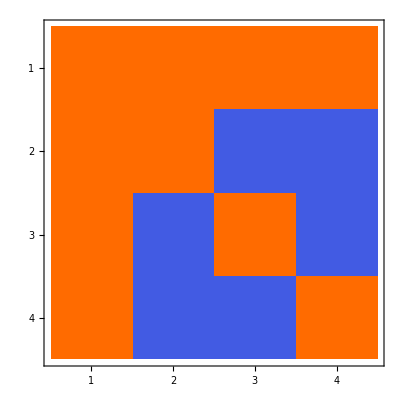
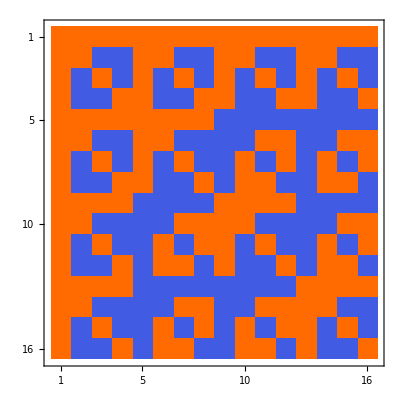
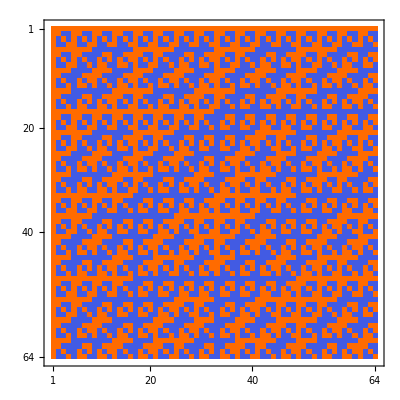
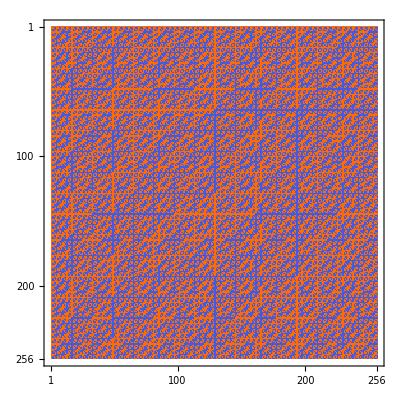

```mathematica
Table[MatrixPlot[tensorPower[a,n]],{n,4}]
```

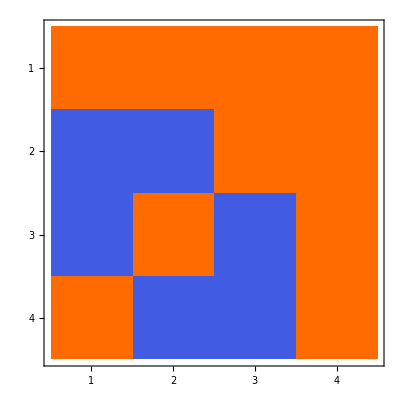
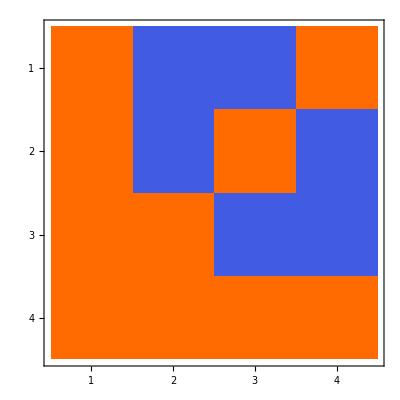

```mathematica
{MatrixPlot[Transpose[Reverse[Transpose[a]]]],MatrixPlot[Reverse[a]]}
```

```mathematica
MatrixPlot[at]
```

-Graphics-

```mathematica
Eigensystem[a]
```

{{-2,2,2,2},{{-1,1,1,1},{1,0,0,1},{1,0,1,0},{1,1,0,0}}}

```mathematica
Eigensystem[at]
```

{{-4,-4,-4,-4,-4,-4,4,4,4,4,4,4,4,4,4,4},{{1,-1,-1,-2,1,-1,-1,0,1,-1,-1,0,0,0,0,1},{-1,1,0,1,0,0,1,0,0,0,1,0,0,0,1,0},{-1,0,1,1,0,1,0,0,0,1,0,0,0,1,0,0},{0,-1,-1,-1,1,0,0,0,1,0,0,0,1,0,0,0},{-1,1,1,1,0,0,0,0,-1,1,1,1,0,0,0,0},{-1,1,1,1,-1,1,1,1,0,0,0,0,0,0,0,0},{-1,-1,-1,0,-1,0,0,0,-1,0,0,0,0,0,0,1},{-1,-1,0,-1,-1,0,0,0,-1,0,0,0,0,0,1,0},{-1,0,-1,-1,-1,0,0,0,-1,0,0,0,0,1,0,0},{2,1,1,1,1,0,0,0,1,0,0,0,1,0,0,0},{1,0,0,1,0,0,0,0,1,0,0,1,0,0,0,0},{1,0,1,0,0,0,0,0,1,0,1,0,0,0,0,0},{1,1,0,0,0,0,0,0,1,1,0,0,0,0,0,0},{1,0,0,1,1,0,0,1,0,0,0,0,0,0,0,0},{1,0,1,0,1,0,1,0,0,0,0,0,0,0,0,0},{1,1,0,0,1,1,0,0,0,0,0,0,0,0,0,0}}}

```mathematica
a
```

{{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}}

```mathematica
b[i_]:=a[[i+1]]
```

```mathematica
b[k_List]:=tensorPower[a,Length[k]][[FromDigits[k,4]+1]]
```

```mathematica
b[{0,1}]
```

{1,1,-1,-1,1,1,-1,-1,1,1,-1,-1,1,1,-1,-1}

```mathematica
Table[
Norm[
Table[
k=IntegerDigits[i,4,n];
Norm[b[k]-Flatten[TensorProduct@@b/@k]],{i,0,Power[4,n]}]],{n,5}]
```

{0,0,0,0,0}

### Definicion a

```mathematica
a={{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}};
```

```mathematica
Needs["Quantum`"]
```

```mathematica
NumberOfParticles=2;
at=tensorPower[a,NumberOfParticles];
```

```mathematica
MatrixForm@at
```

(1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | 1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | -1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | 1
1 | 1 | 1 | 1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1
1 | 1 | -1 | -1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1
1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1
1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | 1 | 1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | 1 | -1
1 | 1 | 1 | 1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | -1 | 1 | 1 | 1 | 1
1 | 1 | -1 | -1 | -1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | 1 | 1 | -1 | -1
1 | -1 | 1 | -1 | -1 | 1 | -1 | 1 | -1 | 1 | -1 | 1 | 1 | -1 | 1 | -1
1 | -1 | -1 | 1 | -1 | 1 | 1 | -1 | -1 | 1 | 1 | -1 | 1 | -1 | -1 | 1)

```mathematica
at[[6]]
```

{1,1,-1,-1,1,1,-1,-1,-1,-1,1,1,-1,-1,1,1}

```mathematica
alpha={1,2}
NumberOfParticles=Length[alpha]
at=tensorPower[a,NumberOfParticles];
```

{1,2}

2

```mathematica
FromDigits[alpha,4]
```

6

```mathematica
at[[FromDigits[alpha,4]]]
```

```mathematica
?Position
```

```mathematica
Phi[alpha_]:=IntegerDigits[#,4,2]&/@(Flatten[Position[at[[FromDigits[alpha,4]]],1]]-1)
```

```mathematica
Phi[alpha]
```

{{0,0},{0,1},{1,0},{1,1},{2,2},{2,3},{3,2},{3,3}}

### Juegos con notacion binaria

```mathematica
(*Single qubit*)
```

```mathematica
p={True}
```

{True}

```mathematica
Copy[p_]:=Flatten[{p,p}]
```

```mathematica
Invert[p_]:=Flatten[{p,Not/@p}]
```

```mathematica
CopyInvert[p_,what_]:=If[what,Copy[p],Invert[p]]
```

```mathematica
Copy[p]
```

{True,True}

```mathematica
ptt=CopyInvert[p,True]
ptf=CopyInvert[p,False]
```

{True,True}

{True,False}

```mathematica
CopyInvert[ptf,True]
```

{True,False,True,False}

```mathematica
vs=Tuples[{0,1},4]
```

{{0,0,0,0},{0,0,0,1},{0,0,1,0},{0,0,1,1},{0,1,0,0},{0,1,0,1},{0,1,1,0},{0,1,1,1},{1,0,0,0},{1,0,0,1},{1,0,1,0},{1,0,1,1},{1,1,0,0},{1,1,0,1},{1,1,1,0},{1,1,1,1}}

### Probando la implementación de la a

```mathematica
NumberOfParticles=7;
at=tensorPower[a,NumberOfParticles];
psiArray=Table[Random[],{Power[4,NumberOfParticles]}];
psiTensor=ArrayReshape[psiArray,ConstantArray[4,NumberOfParticles]];
{Timing[a1=at.psiArray;][[1]],Timing[a2=ApplyAToCuasiparticle[psiTensor];][[1]],Norm[a1-Flatten[a2]]}
```

{1.65017,3.41706,1.21347×10^-11}

```mathematica
MatrixForm/@Table[ApplyAToCuasiparticle[psi,TargetParticle,a],{TargetParticle,0,NumberOfParticles-1}];
```

```mathematica
t={1,0,1,1}
```

{1,0,1,1}

```mathematica
t={1,0,1,1};
FoldList[ApplyAToCuasiparticle,t,{0}]
```

{{1,0,1,1},{3,-1,1,1}}

```mathematica
t={1,1,0,1};
FoldList[ApplyAToCuasiparticle,t,{0}]
```

{{1,1,0,1},{3,1,-1,1}}

```mathematica
Random2QubitPCE[NumberOfInvariants_Integer]:=Normal[SparseArray[Append[RandomSample[Drop[Flatten[Table[{i,j},{i,4},{j,4}],1],1],NumberOfInvariants-1],{1,1}]->1,{4,4}]]
```

```mathematica
t=Random2QubitPCE[8]
```

{{1,0,0,0},{0,1,1,1},{1,0,0,1},{1,0,1,0}}

```mathematica
Table[Random[],{4},{4}]
```

```mathematica
MatrixForm/@FoldList[ApplyAToCuasiparticle,t,{0,1}]
MatrixForm/@FoldList[ApplyAToCuasiparticle,t,{1,0}]
```

{(1 | 0 | 0 | 0
0 | 1 | 1 | 1
1 | 0 | 0 | 1
1 | 0 | 1 | 0),(3 | 1 | 2 | 2
-1 | 1 | 0 | 0
1 | -1 | -2 | 0
1 | -1 | 0 | -2),(3 | 1 | 2 | 2
-1 | 1 | 0 | 0
1 | -1 | -2 | 0
1 | -1 | 0 | -2)}

{(1 | 0 | 0 | 0
0 | 1 | 1 | 1
1 | 0 | 0 | 1
1 | 0 | 1 | 0),(1 | 0 | 0 | 0
0 | 1 | 1 | 1
1 | 0 | 0 | 1
1 | 0 | 1 | 0),(3 | 1 | 2 | 2
-1 | 1 | 0 | 0
1 | -1 | -2 | 0
1 | -1 | 0 | -2)}

```mathematica
t=Table[Random[],{4},{4}];
MatrixForm/@{t,ApplyAToCuasiparticle[t,1]}
```

{(0.400179 | 0.49659 | 0.491206 | 0.31188
0.798898 | 0.852706 | 0.444022 | 0.890996
0.291031 | 0.0388634 | 0.322707 | 0.118936
0.957343 | 0.790625 | 0.640225 | 0.260681),(2.44745 | 2.17878 | 1.89816 | 1.58249
-0.0492971 | 0.519807 | -0.0277037 | 0.823259
-1.06503 | -1.10788 | -0.270334 | -0.720861
0.267593 | 0.395645 | 0.364701 | -0.437372)}

```mathematica
psi=Table[Random[],{4},{4}];
MatrixForm/@{t,ApplyAToCuasiparticle2[psi,1,a]}
```

{(0.6304 | 0.399175 | 0.770471 | 0.452357
0.209632 | 0.676172 | 0.863868 | 0.993199
0.0934769 | 0.676302 | 0.556938 | 0.10082
0.601281 | 0.643883 | 0.0471834 | 0.420883),(2.0385 | 2.08404 | 1.76395 | 2.44891
-0.355389 | 0.0401268 | -0.156357 | 0.811717
0.383811 | 1.24178 | 0.302701 | -0.0929966
-0.0354519 | -0.110568 | -1.42504 | -0.0793937)}

```mathematica
arg=a.(Part[psi,Sequence@@#]&/@i);
Table[psi[[Sequence@@i[[is]]]]=arg[[is]],{is,4}];
```

```mathematica
IntegerDigits[#,4,TargetParticle]&/@(Range[Power[4,TargetParticle]]-1)
```

{{0},{1},{2},{3}}

### Prueba de que al actuar la matriz a sobre particulas individuales, no siempre dan cosas positivicas en el inter

```mathematica
Needs["pce`"]
```

```mathematica
TestPositiveFold[g_,l_]:=And@@(AllTrue[Fold[ApplyAToCuasiparticle,g,#],#≥ 0&,2]&/@l)
```

```mathematica
g=generatorsTwoQubits[[5]]
```

{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}}

```mathematica
MatrixForm/@FoldList[ApplyAToCuasiparticle,g,{0,1}]
MatrixForm/@FoldList[ApplyAToCuasiparticle,g,{1,0}]
```

{(1 | 1 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 1 | 1),(2 | 2 | 0 | 0
2 | 2 | 0 | 0
2 | -2 | 0 | 0
2 | -2 | 0 | 0),(8 | 0 | 0 | 0
0 | 8 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

{(1 | 1 | 0 | 0
1 | 1 | 0 | 0
0 | 0 | 1 | 1
0 | 0 | 1 | 1),(2 | 2 | 2 | 2
2 | 2 | -2 | -2
0 | 0 | 0 | 0
0 | 0 | 0 | 0),(8 | 0 | 0 | 0
0 | 8 | 0 | 0
0 | 0 | 0 | 0
0 | 0 | 0 | 0)}

```mathematica
l=Select[Subsets[Table[i-1,{i,2}]],Length[#]>0&];TestPositiveFold[#,l]&/@generatorsTwoQubits
```

{True,True,True,True,False,False,False,True,False,False,False,True,False,False,False}

### Tablas de desigualdades

```mathematica
tau1=Table[Subscript[τ, i],{i,0,3}];
tau2=Table[Subscript[τ, i,j],{i,0,3},{j,0,3}];
a={{1,1,1,1},{1,1,-1,-1},{1,-1,1,-1},{1,-1,-1,1}};
{a1=a,a2=tensorPower[a1,2]};
```

```mathematica
MatrixForm[a1.Flatten[tau1]]
```

(τ_0+τ_1+τ_2+τ_3
τ_0+τ_1-τ_2-τ_3
τ_0-τ_1+τ_2-τ_3
τ_0-τ_1-τ_2+τ_3)

```mathematica
MatrixForm[a2.Flatten[tau2]]
```

(τ_(0,0)+τ_(0,1)+τ_(0,2)+τ_(0,3)+τ_(1,0)+τ_(1,1)+τ_(1,2)+τ_(1,3)+τ_(2,0)+τ_(2,1)+τ_(2,2)+τ_(2,3)+τ_(3,0)+τ_(3,1)+τ_(3,2)+τ_(3,3)
τ_(0,0)+τ_(0,1)-τ_(0,2)-τ_(0,3)+τ_(1,0)+τ_(1,1)-τ_(1,2)-τ_(1,3)+τ_(2,0)+τ_(2,1)-τ_(2,2)-τ_(2,3)+τ_(3,0)+τ_(3,1)-τ_(3,2)-τ_(3,3)
τ_(0,0)-τ_(0,1)+τ_(0,2)-τ_(0,3)+τ_(1,0)-τ_(1,1)+τ_(1,2)-τ_(1,3)+τ_(2,0)-τ_(2,1)+τ_(2,2)-τ_(2,3)+τ_(3,0)-τ_(3,1)+τ_(3,2)-τ_(3,3)
τ_(0,0)-τ_(0,1)-τ_(0,2)+τ_(0,3)+τ_(1,0)-τ_(1,1)-τ_(1,2)+τ_(1,3)+τ_(2,0)-τ_(2,1)-τ_(2,2)+τ_(2,3)+τ_(3,0)-τ_(3,1)-τ_(3,2)+τ_(3,3)
τ_(0,0)+τ_(0,1)+τ_(0,2)+τ_(0,3)+τ_(1,0)+τ_(1,1)+τ_(1,2)+τ_(1,3)-τ_(2,0)-τ_(2,1)-τ_(2,2)-τ_(2,3)-τ_(3,0)-τ_(3,1)-τ_(3,2)-τ_(3,3)
τ_(0,0)+τ_(0,1)-τ_(0,2)-τ_(0,3)+τ_(1,0)+τ_(1,1)-τ_(1,2)-τ_(1,3)-τ_(2,0)-τ_(2,1)+τ_(2,2)+τ_(2,3)-τ_(3,0)-τ_(3,1)+τ_(3,2)+τ_(3,3)
τ_(0,0)-τ_(0,1)+τ_(0,2)-τ_(0,3)+τ_(1,0)-τ_(1,1)+τ_(1,2)-τ_(1,3)-τ_(2,0)+τ_(2,1)-τ_(2,2)+τ_(2,3)-τ_(3,0)+τ_(3,1)-τ_(3,2)+τ_(3,3)
τ_(0,0)-τ_(0,1)-τ_(0,2)+τ_(0,3)+τ_(1,0)-τ_(1,1)-τ_(1,2)+τ_(1,3)-τ_(2,0)+τ_(2,1)+τ_(2,2)-τ_(2,3)-τ_(3,0)+τ_(3,1)+τ_(3,2)-τ_(3,3)
τ_(0,0)+τ_(0,1)+τ_(0,2)+τ_(0,3)-τ_(1,0)-τ_(1,1)-τ_(1,2)-τ_(1,3)+τ_(2,0)+τ_(2,1)+τ_(2,2)+τ_(2,3)-τ_(3,0)-τ_(3,1)-τ_(3,2)-τ_(3,3)
τ_(0,0)+τ_(0,1)-τ_(0,2)-τ_(0,3)-τ_(1,0)-τ_(1,1)+τ_(1,2)+τ_(1,3)+τ_(2,0)+τ_(2,1)-τ_(2,2)-τ_(2,3)-τ_(3,0)-τ_(3,1)+τ_(3,2)+τ_(3,3)
τ_(0,0)-τ_(0,1)+τ_(0,2)-τ_(0,3)-τ_(1,0)+τ_(1,1)-τ_(1,2)+τ_(1,3)+τ_(2,0)-τ_(2,1)+τ_(2,2)-τ_(2,3)-τ_(3,0)+τ_(3,1)-τ_(3,2)+τ_(3,3)
τ_(0,0)-τ_(0,1)-τ_(0,2)+τ_(0,3)-τ_(1,0)+τ_(1,1)+τ_(1,2)-τ_(1,3)+τ_(2,0)-τ_(2,1)-τ_(2,2)+τ_(2,3)-τ_(3,0)+τ_(3,1)+τ_(3,2)-τ_(3,3)
τ_(0,0)+τ_(0,1)+τ_(0,2)+τ_(0,3)-τ_(1,0)-τ_(1,1)-τ_(1,2)-τ_(1,3)-τ_(2,0)-τ_(2,1)-τ_(2,2)-τ_(2,3)+τ_(3,0)+τ_(3,1)+τ_(3,2)+τ_(3,3)
τ_(0,0)+τ_(0,1)-τ_(0,2)-τ_(0,3)-τ_(1,0)-τ_(1,1)+τ_(1,2)+τ_(1,3)-τ_(2,0)-τ_(2,1)+τ_(2,2)+τ_(2,3)+τ_(3,0)+τ_(3,1)-τ_(3,2)-τ_(3,3)
τ_(0,0)-τ_(0,1)+τ_(0,2)-τ_(0,3)-τ_(1,0)+τ_(1,1)-τ_(1,2)+τ_(1,3)-τ_(2,0)+τ_(2,1)-τ_(2,2)+τ_(2,3)+τ_(3,0)-τ_(3,1)+τ_(3,2)-τ_(3,3)
τ_(0,0)-τ_(0,1)-τ_(0,2)+τ_(0,3)-τ_(1,0)+τ_(1,1)+τ_(1,2)-τ_(1,3)-τ_(2,0)+τ_(2,1)+τ_(2,2)-τ_(2,3)+τ_(3,0)-τ_(3,1)-τ_(3,2)+τ_(3,3))

```mathematica
Power[2,15]
```

32768

```mathematica
MatrixForm[a]
```

(1 | 1 | 1 | 1
1 | 1 | -1 | -1
1 | -1 | 1 | -1
1 | -1 | -1 | 1)

```mathematica
a.{0,1,1,1}
a.{1,0,1,1}
```

{3,-1,-1,-1}

{3,-1,1,1}

### Probando el paquete de Jose Alfredo

```mathematica
Needs["pce`"]
```

```mathematica
generatorsTwoQubits=ArrayReshape[Diagonal/@PCEgenerators[2],{15,4,4}];
Composition2=Union[Times@@@Subsets[generatorsTwoQubits,{2}]];
```

```mathematica
(*Ejemplos simples*)
ApplyAToCuasiparticle/@generatorsTwoQubits;
FromSigmaNotationToGenerator[{2,3}];
```

```mathematica
(*Verificaciones*)

(*Verifico que la notacion de indices y sigmas funciona de manera bijectiva*)
And@@Table[
Digits=IntegerDigits[i,4,2];ToSigmaNotation[FromSigmaNotationToGenerator[Digits]]==Digits,{i,0,15}]
```

True

```mathematica
(*Acá cuento cuantos elementos de los generadores aparecen contribuyendo a cada elemento en particular de los uqe dejan 4 componentes invariantes. *)
TablaConGeneradores=Table[ToSigmaNotation/@Select[generatorsTwoQubits,SubsetQ[Position[#,1],Position[g,1]]&],{g,Composition2}];
Table[Length[Select[TablaConGeneradores,MemberQ[#,{i,j}]&]],{i,0,3},{j,0,3}]
```

{{0,7,7,7},{7,7,7,7},{7,7,7,7},{7,7,7,7}}

```mathematica
GeneratorPlot[g_]:=Show[{ArrayPlot[g,ImageSize->60],Graphics[Text[Style[ToString[ToSigmaNotation[g]],Large,Red],Scaled[{.5,.5}]]]}]
Leave4Plot[g_]:={Show[{ArrayPlot[g,ImageSize->60],Graphics[Text[Style[ToString[Position[Composition2,g][[1,1]]],Large,Red],Scaled[{.5,.5}]]]}],GeneratorPlot/@(Select[generatorsTwoQubits,SubsetQ[Position[#,1],Position[g,1]]&])}
```

```mathematica
Table[GeneratorPlot[g],{g,generatorsTwoQubits}]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Leave4Plot/@Composition2
```

{{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}}}

```mathematica
PositionInList=Position[Composition2,g][[1,1]];
```

```mathematica
g8=generatorsTwoQubits[[5]]
g4=Composition2[[5]]
```

{{1,1,0,0},{1,1,0,0},{0,0,1,1},{0,0,1,1}}

{{1,0,0,0},{0,0,1,0},{0,0,0,1},{0,1,0,0}}

```mathematica
b={ts=IntegerDigits[#,2,4];
#,ts,(a.ts)}&/@Range[0,15]
```

{{0,{0,0,0,0},{0,0,0,0}},{1,{0,0,0,1},{1,-1,-1,1}},{2,{0,0,1,0},{1,-1,1,-1}},{3,{0,0,1,1},{2,-2,0,0}},{4,{0,1,0,0},{1,1,-1,-1}},{5,{0,1,0,1},{2,0,-2,0}},{6,{0,1,1,0},{2,0,0,-2}},{7,{0,1,1,1},{3,-1,-1,-1}},{8,{1,0,0,0},{1,1,1,1}},{9,{1,0,0,1},{2,0,0,2}},{10,{1,0,1,0},{2,0,2,0}},{11,{1,0,1,1},{3,-1,1,1}},{12,{1,1,0,0},{2,2,0,0}},{13,{1,1,0,1},{3,1,-1,1}},{14,{1,1,1,0},{3,1,1,-1}},{15,{1,1,1,1},{4,0,0,0}}}

```mathematica
MatrixForm[Select[b,And@@Thread[#[[3]]≥0]&]]
```

(0 | {0,0,0,0} | {0,0,0,0}
8 | {1,0,0,0} | {1,1,1,1}
9 | {1,0,0,1} | {2,0,0,2}
10 | {1,0,1,0} | {2,0,2,0}
12 | {1,1,0,0} | {2,2,0,0}
15 | {1,1,1,1} | {4,0,0,0})

```mathematica
list2generators=Flatten[Table[{{i,j},Position[Composition2,Times[generatorsTwoQubits[[i]],generatorsTwoQubits[[j]]]][[1,1]]},{i,Length[generatorsTwoQubits]},{j,i+1,Length[generatorsTwoQubits]}],1];
GeneradoresPorProducto=Map[First,Sort[GatherBy[list2generators,Last],#1[[1,2]]<#2[[1,2]]&],{2}];
```

```mathematica
All3Sets=Subsets[generatorsTwoQubits,{3}];
```

```mathematica
All3SetsCombined=Times@@@All3Sets;
```

```mathematica
Composition3=Union[Times@@@Subsets[generatorsTwoQubits,{3}]];
```

```mathematica
g2=Composition3[[14]]
```

{{1,0,0,0},{0,0,1,0},{0,0,0,0},{0,0,0,0}}

```mathematica
(*Ejemplo de las combinaciones de generadores uqe me dan un elemento*)elements3=Map[ToSigmaNotation,All3Sets[[Flatten[Position[All3SetsCombined,Composition3[[14]]]]]],{2}];
(*Todas los generadores aparecen el mismo numero de veces*)
Tally[Flatten[elements3,1]]
```

{{{2,0},12},{{0,1},12},{{1,2},12},{{3,2},12},{{1,3},12},{{3,3},12},{{2,1},12}}

```mathematica
AllCombinationsGeneratosComposition2=Outer[Times,generatorsTwoQubits,Composition2,1,1];
```

```mathematica
Position[AllCombinationsGeneratosComposition2,g]
```

{{2,5},{2,7},{2,21},{2,33},{4,5},{4,6},{4,7},{4,8},{6,6},{6,8},{6,21},{6,33},{9,5},{9,6},{9,21},{9,28},{11,6},{11,7},{11,28},{11,33},{13,7},{13,8},{13,21},{13,28},{15,5},{15,8},{15,28},{15,33}}

```mathematica
(*Ordenados por el generador*)Sort[Position[AllCombinationsGeneratosComposition2,g]]
```

{{2,5},{2,7},{2,21},{2,33},{4,5},{4,6},{4,7},{4,8},{6,6},{6,8},{6,21},{6,33},{9,5},{9,6},{9,21},{9,28},{11,6},{11,7},{11,28},{11,33},{13,7},{13,8},{13,21},{13,28},{15,5},{15,8},{15,28},{15,33}}

```mathematica
(*Ordenados por el que deja cuatro*)
Sort[Position[AllCombinationsGeneratosComposition2,g],#1[[2]]<#2[[2]]&]
```

{{15,5},{9,5},{4,5},{2,5},{11,6},{9,6},{6,6},{4,6},{13,7},{11,7},{4,7},{2,7},{15,8},{13,8},{6,8},{4,8},{13,21},{9,21},{6,21},{2,21},{15,28},{13,28},{11,28},{9,28},{15,33},{11,33},{6,33},{2,33}}

```mathematica
(*Formas en que se puede componer para generar un bicho*)
g=Composition3[[14]];
{ArrayPlot[g,ImageSize->60],Leave4Plot[Composition2[[#[[2]]]]],GeneratorPlot[generatorsTwoQubits[[#[[1]]]]]}&/@Sort[Position[AllCombinationsGeneratosComposition2,g]]
```

{{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-},{-Graphics-,{-Graphics-,{-Graphics-,-Graphics-,-Graphics-}},-Graphics-}}

```mathematica
{x1,x2}={28292.21,16969.32}
```

{28292.2,16969.3}

```mathematica
{x2/x1,x1-x2}
```

{0.599788,11322.9}

```mathematica
11312.89
```

```mathematica
ArrayPlot[#,ImageSize->100]&/@Composition3
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
ToBinary[g_]:={g[[1,2]],g[[1,3]],g[[2,1]],g[[3,1]]}
ToBinaryString[g_]:=StringJoin[ToString/@ToBinary[g]]
To4ry[g_]:=FromDigits[#,2]&/@{{g[[1,2]],g[[1,3]]},{g[[2,1]],g[[3,1]]}}
To4String[g_]:=StringJoin[ToString/@To4ry[g]]
```